```mathematica
(* https://www.expii.com/solve/20/5 *)
(* After a deep hundred year slumber, Ant the ant wakes up in an unfamiliar,large, dark square forest. Ant is unaware of its exact location or direction,but it does know that its starting point is exactly 1 meter away from the nearest straight edge. What is the shortest distance Ant must travel to guarantee escape from the forest? Round your answer, in meters to the nearest hundredth. *)
```

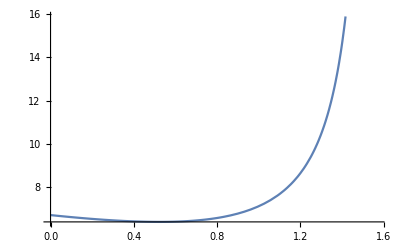

{6.39724,{theta→0.523599}}

```mathematica
(* Walking further than 1m, going to a point on a circle (r=1m) so it touches it tangentially, walk on the circle until you reach the other side and then move tangentially for 1m until you cross the mirror of the first tangential line ... *)
d[theta_]=Sqrt[1+Tan[theta]^2]+Tan[theta]+2*(Pi/2-theta) + Pi/2  + 1;
Plot[d[theta],{theta,0,Pi/2}]
FindMinimum[d[theta],{theta,0.3}]
```